# Frobenius solutions of Radial Teukolsky ODE

```mathematica
Delta[r_] := 1-2M/r
Delta[r]
D[Delta[r], r]
```

1-2/r

2/r^2

Define the functions appearing in the Teukolsky Radial ODE:

```mathematica
a = 0 
F[r_]:= D[Delta[r],r]
G[r_]:= ((1-a^2/L^2)^2)*(ω(r^2+a^2)-a*m)^2-ⅈ*s*((1-a^2/L^2))*(ω(r^2+a^2)-a*m)*D[Delta[r],r] 
H[r_] := ⅈ*4*s*ω*((1-a^2/L^2))*r+2/(L^2)(μ+3s+2s^2)*r^2+s*(1+a^2/L^2)-λ+2*(1-a^2/L^2)^2*a*m*ω-a^2*(1-a^2/L^2)^2*ω^2
```

0

```mathematica
F[r]
G[r]
H[r]
```

(2 M)/r^2

-2 ⅈ M s ω+r^4 ω^2

s-λ+(2 r^2 (3 s+2 s^2+μ))/L^2+4 ⅈ r s ω

Use “Seriescoefficient” to extract the series coefficients of the power series expansions around r=h:

```mathematica
Fj[j_] := SeriesCoefficient[F[r], {r, h, j}]
Gj[j_] := SeriesCoefficient[G[r], {r, h, j}]
Hj[j_] := SeriesCoefficient[H[r], {r, h, j}]
```

Compute the coefficients we need to define the indicial polynomial:

```mathematica
Fj0[j_] := SeriesCoefficient[F[r], {r, h, j}]
Gj0[j_] := SeriesCoefficient[G[r], {r, h, j}]
Hj0[j_] := SeriesCoefficient[H[r], {r, h, j}]

Fj0[0]
Gj0[0]
Hj0[0]
```

(2 M)/h^2

ω (-2 ⅈ M s+h^4 ω)

s-λ+(2 h^2 (3 s+2 s^2+μ))/L^2+4 ⅈ h s ω

Define indicial polynomial:

```mathematica
F0 = Fj0[0]
G0 = Gj0[0]
Q[n_] := n*(n-1) + F0*n + G0
Q[n]
```

(2 M)/h^2

ω (-2 ⅈ M s+h^4 ω)

(2 M n)/h^2+(-1+n) n+ω (-2 ⅈ M s+h^4 ω)

```mathematica
h = 2*M
indicialroots = Solve[Q[n]==0, n]
n1 = n/.indicialroots[[1]]
n2 = n/.indicialroots[[2]]
```

2 M

{{n→1/4 (2-1/M-(√(1-4 M+4 M^2+32 ⅈ M^3 s ω-256 M^6 ω^2))/M)},{n→1/4 (2-1/M+(√(1-4 M+4 M^2+32 ⅈ M^3 s ω-256 M^6 ω^2))/M)}}

1/4 (2-1/M-(√(1-4 M+4 M^2+32 ⅈ M^3 s ω-256 M^6 ω^2))/M)

1/4 (2-1/M+(√(1-4 M+4 M^2+32 ⅈ M^3 s ω-256 M^6 ω^2))/M)

Set up the recursion to find the coefficients:

```mathematica
A[0] = A0
A[k_] := A[k] = -Sum[((n1+i)*Fj0[k-i]+Gj0[k-i])*A[i],{i, 0, k-1}]/Q[n1+k]
```

A0

1

0

6

1

4

((-512+1/8 (1-3 ⅈ √455)) (-2+r)^((1+8 ⅈ)+1/4 (1-3 ⅈ √455)))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))+((-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))) (-2+r)^((2+8 ⅈ)+1/4 (1-3 ⅈ √455)))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))+((-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))) (-2+r)^((3+8 ⅈ)+1/4 (1-3 ⅈ √455)))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))+((-16-5/128 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (128+1/4 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((384+3/8 (2+1/4 (1-3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))-((512+1/2 (-3+1/4 (-1+3 ⅈ √455))) (-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))) (-2+r)^((4+8 ⅈ)+1/4 (1-3 ⅈ √455)))/(256+1/2 (4+1/4 (1-3 ⅈ √455))+(3+1/4 (1-3 ⅈ √455)) (4+1/4 (1-3 ⅈ √455)))+((3/128 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (16+5/32 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((128+1/4 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))-((384+3/8 (3+1/4 (1-3 ⅈ √455))) (-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))-((512+1/2 (-4+1/4 (-1+3 ⅈ √455))) (-16-5/128 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (128+1/4 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((384+3/8 (2+1/4 (1-3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))-((512+1/2 (-3+1/4 (-1+3 ⅈ √455))) (-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))))/(256+1/2 (4+1/4 (1-3 ⅈ √455))+(3+1/4 (1-3 ⅈ √455)) (4+1/4 (1-3 ⅈ √455)))) (-2+r)^((5+8 ⅈ)+1/4 (1-3 ⅈ √455)))/(256+1/2 (5+1/4 (1-3 ⅈ √455))+(4+1/4 (1-3 ⅈ √455)) (5+1/4 (1-3 ⅈ √455)))+((-7/512 (1-3 ⅈ √455)+(3 (-512+1/8 (1-3 ⅈ √455)) (1+1/4 (1-3 ⅈ √455)))/(32 (256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455))))-((16+5/32 (2+1/4 (1-3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))-((128+1/4 (-3+1/4 (-1+3 ⅈ √455))) (-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))-((384+3/8 (4+1/4 (1-3 ⅈ √455))) (-16-5/128 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (128+1/4 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((384+3/8 (2+1/4 (1-3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))-((512+1/2 (-3+1/4 (-1+3 ⅈ √455))) (-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))))/(256+1/2 (4+1/4 (1-3 ⅈ √455))+(3+1/4 (1-3 ⅈ √455)) (4+1/4 (1-3 ⅈ √455)))-((512+1/2 (-5+1/4 (-1+3 ⅈ √455))) (3/128 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (16+5/32 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((128+1/4 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))-((384+3/8 (3+1/4 (1-3 ⅈ √455))) (-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))-((512+1/2 (-4+1/4 (-1+3 ⅈ √455))) (-16-5/128 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (128+1/4 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((384+3/8 (2+1/4 (1-3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))-((512+1/2 (-3+1/4 (-1+3 ⅈ √455))) (-128+1/16 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (384+3/8 (1+1/4 (1-3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))-((512+1/2 (-2+1/4 (-1+3 ⅈ √455))) (-384-3/32 (1-3 ⅈ √455)-((-512+1/8 (1-3 ⅈ √455)) (512+1/2 (-1+1/4 (-1+3 ⅈ √455))))/(256+1/2 (1+1/4 (1-3 ⅈ √455))+1/4 (1-3 ⅈ √455) (1+1/4 (1-3 ⅈ √455)))))/(256+1/2 (2+1/4 (1-3 ⅈ √455))+(1+1/4 (1-3 ⅈ √455)) (2+1/4 (1-3 ⅈ √455)))))/(256+1/2 (3+1/4 (1-3 ⅈ √455))+(2+1/4 (1-3 ⅈ √455)) (3+1/4 (1-3 ⅈ √455)))))/(256+1/2 (4+1/4 (1-3 ⅈ √455))+(3+1/4 (1-3 ⅈ √455)) (4+1/4 (1-3 ⅈ √455)))))/(256+1/2 (5+1/4 (1-3 ⅈ √455))+(4+1/4 (1-3 ⅈ √455)) (5+1/4 (1-3 ⅈ √455)))) (-2+r)^((6+8 ⅈ)+1/4 (1-3 ⅈ √455)))/(256+1/2 (6+1/4 (1-3 ⅈ √455))+(5+1/4 (1-3 ⅈ √455)) (6+1/4 (1-3 ⅈ √455)))

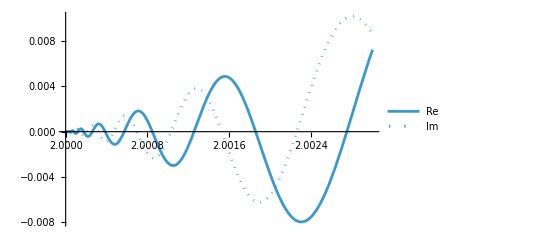

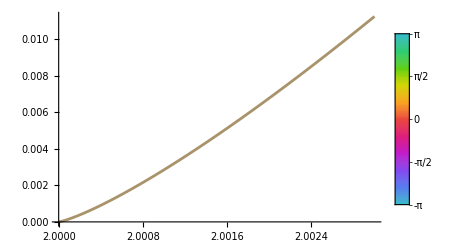

```mathematica
A0 = 1
s = 0
k = 6
M = 1
ω = 4

Sum[A[j]*(r-h)^(j+n1+2*M*ω*ⅈ), {j, k}]
ReImPlot[Normal[Sum[A[j]*(r-h)^(j+n1+2*M*ω*ⅈ), {j, k}]], {r, h, h+0.003}, PlotLegends->Automatic]
AbsArgPlot[Normal[Sum[A[j]*(r-h)^(j+n1+2*M*ω*ⅈ), {j, k}]], {r, h, h+0.003}, PlotLegends->Automatic]
```